```mathematica
alanineFull = Import[NotebookDirectory[]<>"../code/ops/AD_initial_frame.pdb",  "Molecule"];
MoleculePlot3D[alanine];
```

-Graphics3D-

```mathematica
alanine = Import[NotebookDirectory[]<>"../code/AD_initial_frame.pdb"]
alanine = Import[NotebookDirectory[]<>"../code/output.pdb"]
```

-Graphics3D-

-Graphics3D-

```mathematica
alanineMolecule = ConnectedMoleculeComponents[alanineFull][[1]]
```

Molecule[…]

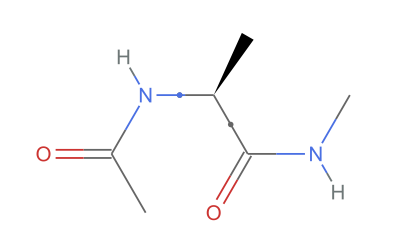

```mathematica
MoleculePlot[alanineMolecule, BondLabels->{Bond[{7, 9}]->MaTeX["\phi", FontSize->28], Bond[{9, 15}]->MaTeX["\psi", FontSize->28 ]},BondLabelStyle->Directive[FontSize->20, Purple],  PlotTheme->"Aromatic"]
```

```mathematica
MoleculeRecognize[%]
```

Molecule[…]

```mathematica
<<MaTeX`
```

```mathematica
https://www.wolfram.com/language/12/molecular-structure-and-computation/torsional-potential-energy-surface-of-butane.html.en?product=mathematica
```